```mathematica
pressure[r_,r0_,τ_,E_]:=E τ r0 (r-r0)/r^3
```

```mathematica
pressureLaplace[r_,r0_,τ_,E_]:=((E τ)/r0)(r/r0-1)
```

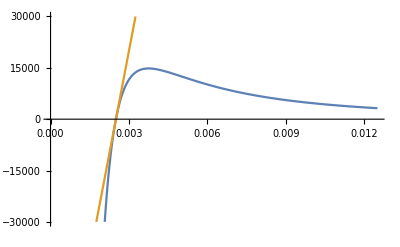

```mathematica
Plot[{
pressure[r,2.5 10^-3,0.5 10^-3,500000],
pressureLaplace[r,2.5 10^-3,0.5 10^-3,500000]
},{r,0,5 2.5 10^-3},PlotRange->{-30000,30000}]
```

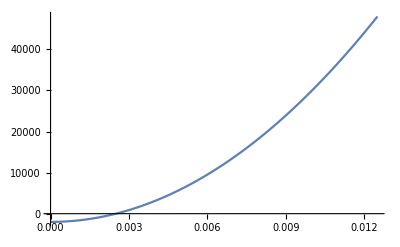

```mathematica
tubeLaw[r_,r0_,P0_,n_]:=P0(1-(r/r0)^(2/n))
Plot[tubeLaw[r,2.5 10^-3,-2000,1],{r,0,5 2.5 10^-3}]
```

```mathematica
D[tubeLaw[r,r0,P0,n],r]//Simplify
%/.{r->r0}
D[pressure[r,r0,τ,Y],r]//Simplify
%/.{r->r0}
Solve[%%%==%,n]
```

-(2 P0 (r/r0)^(2/n))/(n r)

-(2 P0)/(n r0)

-((2 r-3 r0) r0 Y τ)/r^4

(Y τ)/r0^2

{{n→-(2 P0 r0)/(Y τ)}}

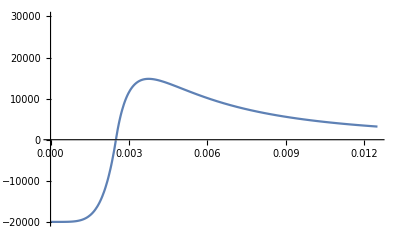

```mathematica
With[{r0=2.5 10^-3,τ=0.5 10^-3,E=500000,P0=-20000},Plot[
If[r<r0,tubeLaw[r,r0,-P0,(-2 P0 r0)/(E τ)],pressure[r,r0,τ,E]]
,{r,0,5r0},PlotRange->{-20000,30000}]]
```

## Inverse of pressure curve

(-1+r)/r^3

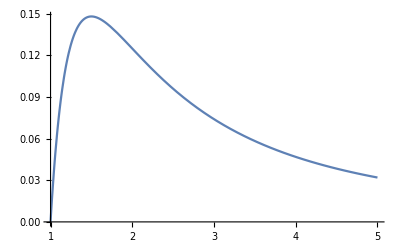

{{r→-((2/3)^(1/3) r0 t y)/((9 P^2 r0^2 t y+√3 √(27 P^4 r0^4 t^2 y^2-4 P^3 r0^3 t^3 y^3))^(1/3))-((9 P^2 r0^2 t y+√3 √(27 P^4 r0^4 t^2 y^2-4 P^3 r0^3 t^3 y^3))^(1/3))/(2^(1/3) 3^(2/3) P)},{r→((1+ⅈ √3) r0 t y)/(2^(2/3) 3^(1/3) (9 P^2 r0^2 t y+√3 √(27 P^4 r0^4 t^2 y^2-4 P^3 r0^3 t^3 y^3))^(1/3))+((1-ⅈ √3) (9 P^2 r0^2 t y+√3 √(27 P^4 r0^4 t^2 y^2-4 P^3 r0^3 t^3 y^3))^(1/3))/(2 2^(1/3) 3^(2/3) P)},{r→((1-ⅈ √3) r0 t y)/(2^(2/3) 3^(1/3) (9 P^2 r0^2 t y+√3 √(27 P^4 r0^4 t^2 y^2-4 P^3 r0^3 t^3 y^3))^(1/3))+((1+ⅈ √3) (9 P^2 r0^2 t y+√3 √(27 P^4 r0^4 t^2 y^2-4 P^3 r0^3 t^3 y^3))^(1/3))/(2 2^(1/3) 3^(2/3) P)}}

{{r→-(2/3)^(1/3)/((9 P^2+√3 √(-4 P^3+27 P^4))^(1/3))-((9 P^2+√3 √(-4 P^3+27 P^4))^(1/3))/(2^(1/3) 3^(2/3) P)},{r→(1+ⅈ √3)/(2^(2/3) 3^(1/3) (9 P^2+√3 √(-4 P^3+27 P^4))^(1/3))+((1-ⅈ √3) (9 P^2+√3 √(-4 P^3+27 P^4))^(1/3))/(2 2^(1/3) 3^(2/3) P)},{r→(1-ⅈ √3)/(2^(2/3) 3^(1/3) (9 P^2+√3 √(-4 P^3+27 P^4))^(1/3))+((1+ⅈ √3) (9 P^2+√3 √(-4 P^3+27 P^4))^(1/3))/(2 2^(1/3) 3^(2/3) P)}}

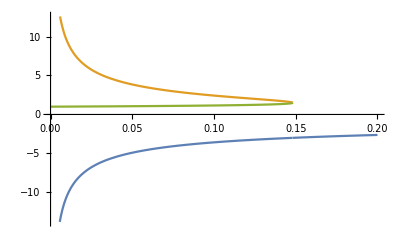

(1+ⅈ √3)/(2^(2/3) 3^(1/3) (9 P^2+√3 √(-4 P^3+27 P^4))^(1/3))+((1-ⅈ √3) (9 P^2+√3 √(-4 P^3+27 P^4))^(1/3))/(2 2^(1/3) 3^(2/3) P)

2.42362-2.22045×10^-16 ⅈ

```mathematica
pressure[r,1,1,1]
Plot[%,{r,1,5}]
Solve[pressure[r,r0,t,y]==P,r]
%/.{r0->1,t->1,y->1}
Plot[Evaluate[%[[All,1,2]]],{P,0,0.2}]
%%[[2,1,2]]
%/.{P->0.1}
```

## Appendix

```mathematica
pressureSlopeR0[r0_,t_,y_]:=t y/r0^2
pressureSlopeR0[0.010,0.001,1000000]
```

1.×10^7

-9.×10^7

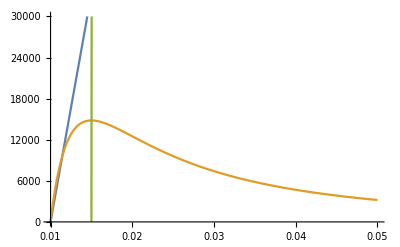

```mathematica
pressure[0.001,0.010,0.001,1000000]
Plot[{
(r-0.010) pressureSlopeR0[0.010,0.001,1000000]/1.5,
pressure[r,0.010,0.001,1000000],
10^9(r-(3 0.010)/2)
},{r,0.01,0.05},PlotRange->{0,30000}]
```

```mathematica
Series[pressure[r,r0,t,y],{r,r0,2}]
Solve[Normal[%]==P,r]
Solve[(t y (r-r0))/r0^2==P,r]
```

(t y (r-r0))/r0^2-(3 (t y) (r-r0)^2)/r0^3+O[r-r0]^3

{{r→(7 r0 t y-r0 √(-12 P r0 t y+t^2 y^2))/(6 t y)},{r→(7 r0 t y+r0 √(-12 P r0 t y+t^2 y^2))/(6 t y)}}

{{r→(r0 (P r0+t y))/(t y)}}

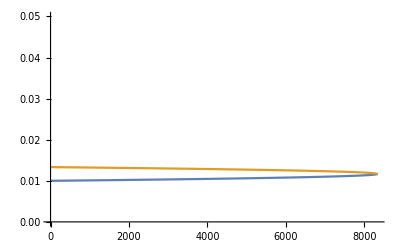

```mathematica
With[{r0=0.010,t=0.001,y=1000000},Plot[{
(7 r0 t y-r0 √(-12 P r0 t y+t^2 y^2))/(6 t y),
(7 r0 t y+r0 √(-12 P r0 t y+t^2 y^2))/(6 t y)
},{P,0,20000},PlotRange->{0,0.05}]]
```

```mathematica
D[pressure[r,r0,t,y],r]//Factor
Solve[%==0,r]
pressure[r,r0,t,y]/.%
n π r^2 L/.%%
```

-((2 r-3 r0) r0 t y)/r^4

{{r→(3 r0)/2}}

{(4 t y)/(27 r0)}

{9/4 L n π r0^2}

```mathematica
N[(4 t y)/(27 r0)/.{t->0.001,y->10^6,r0->0.005},30]
9/4 L n π r0^2/.{L->1,r0->0.005,n->1}
```

29629.6

0.000176715

## Derivatives

```mathematica
D[pressure[√(V/(π L)),r0,t,y],V]//Simplify
FullSimplify[
%,
Assumptions->{V>0,L>0,r0>0,t>0,y>0}
]
```

(L π r0 t (-2 V+3 L √π r0 √(V/L)) y)/(2 V^3)

(L π r0 t (-2 V+3 √π r0 √(L V)) y)/(2 V^3)

## Pressure model without wall thinning

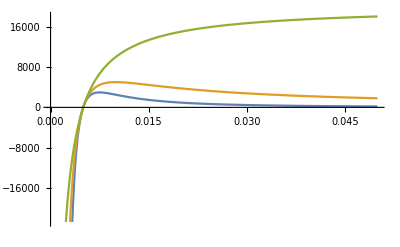

```mathematica
balloonPressure[r_,r0_,τ_,E_]:=E τ r0 (r-r0)/r^3
thickWallPressure[r_,r0_,τ_,E_]:=E τ (r-r0)/r^2
With[{r0=0.005},
Plot[{
balloonPressure[r,r0,0.001,100000],
thickWallPressure[r,r0,0.001,100000],
100000 0.001 (r-r0)/(r r0)
},{r,0,10r0}]]
```

```mathematica
Solve[100000 0.001 (r-r0)/(r r0)==P,r]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r→-(100. r0)/(-100.+P r0)}}